```mathematica
names={"prog1.txt","prog2.txt","prog3.txt"};
imp=Table[Import[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>names[[i]],"Table"],{i,1,Length[names]}];
data=imp
```

{{{510.38,20648.4},{511.39,21416.2},{512.31,22169.8},{513.12,22594.8},{514.23,24139.3},{515.55,24918.6},{516.75,25676.8},{518.06,26152.2},{519.36,27342.},{520.86,28514.8},{522.45,28514.1},{524.03,30137.6},{525.52,31489.5},{527.29,32406.1},{528.95,33866.4},{530.91,36006.5},{532.95,36370.8},{534.88,37365.},{536.81,38085.2},{539.11,37937.6},{541.3,37900.8},{543.48,38449.9},{545.74,39060.8},{548.18,40202.9},{550.78,41168.5},{553.37,43897.2},{556.22,43105.3},{558.86,43389.9},{561.84,44442.5},{564.62,44223.9}},{{545.27,40795.2},{547.43,42538.1},{549.95,43011.8},{552.36,43579.},{554.75,43685.8},{557.31,43573.6},{559.86,44733.5},{562.74,43093.5},{565.51,42056.3},{568.53,41244.5},{571.61,40516.4},{574.74,39839.5},{578.1,38753.1},{581.6,38001.},{584.97,37887.3},{588.39,36955.},{592.1,37770.3},{595.84,37995.2},{599.77,39063.6},{603.56,39868.5},{607.45,40721.4},{611.58,41522.3}},{{569.41,44092.},{572.13,42262.5},{575.35,40850.6},{578.45,39297.2},{581.77,38222.6},{585.23,38104.4},{588.64,37136.5},{592.1,37770.3},{595.84,37995.2},{599.61,38881.9},{603.4,39959.7},{607.45,40721.4},{611.43,41704.9}}}

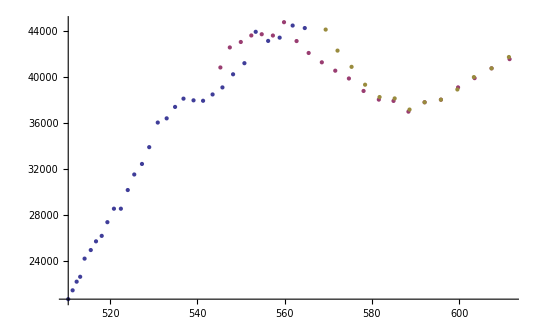

```mathematica
ListPlot[data]
```

```mathematica
ν0=Table[{48-i,data[[1,i,1]]},{i,1,Length[data[[1]]]}]
ν1=Table[{28-i,data[[2,i,1]]},{i,1,Length[data[[2]]]}]
ν2=Table[{19-i,data[[3,i,1]]},{i,1,Length[data[[3]]]}]
ν0[[All,2]]=10^7/ν0[[All,2]];
ν1[[All,2]]=10^7/ν1[[All,2]];
ν2[[All,2]]=10^7/ν2[[All,2]];
ν0
ν1
ν2
```

{{47,510.38},{46,511.39},{45,512.31},{44,513.12},{43,514.23},{42,515.55},{41,516.75},{40,518.06},{39,519.36},{38,520.86},{37,522.45},{36,524.03},{35,525.52},{34,527.29},{33,528.95},{32,530.91},{31,532.95},{30,534.88},{29,536.81},{28,539.11},{27,541.3},{26,543.48},{25,545.74},{24,548.18},{23,550.78},{22,553.37},{21,556.22},{20,558.86},{19,561.84},{18,564.62}}

{{27,545.27},{26,547.43},{25,549.95},{24,552.36},{23,554.75},{22,557.31},{21,559.86},{20,562.74},{19,565.51},{18,568.53},{17,571.61},{16,574.74},{15,578.1},{14,581.6},{13,584.97},{12,588.39},{11,592.1},{10,595.84},{9,599.77},{8,603.56},{7,607.45},{6,611.58}}

{{18,569.41},{17,572.13},{16,575.35},{15,578.45},{14,581.77},{13,585.23},{12,588.64},{11,592.1},{10,595.84},{9,599.61},{8,603.4},{7,607.45},{6,611.43}}

{{47,19593.2},{46,19554.5},{45,19519.4},{44,19488.6},{43,19446.6},{42,19396.8},{41,19351.7},{40,19302.8},{39,19254.5},{38,19199.},{37,19140.6},{36,19082.9},{35,19028.8},{34,18964.9},{33,18905.4},{32,18835.6},{31,18763.5},{30,18695.8},{29,18628.6},{28,18549.1},{27,18474.},{26,18399.9},{25,18323.7},{24,18242.2},{23,18156.1},{22,18071.1},{21,17978.5},{20,17893.6},{19,17798.7},{18,17711.}}

{{27,18339.5},{26,18267.2},{25,18183.5},{24,18104.1},{23,18026.1},{22,17943.3},{21,17861.6},{20,17770.2},{19,17683.2},{18,17589.2},{17,17494.4},{16,17399.2},{15,17298.},{14,17193.9},{13,17094.9},{12,16995.5},{11,16889.},{10,16783.},{9,16673.1},{8,16568.4},{7,16462.3},{6,16351.1}}

{{18,17562.},{17,17478.5},{16,17380.7},{15,17287.6},{14,17188.9},{13,17087.3},{12,16988.3},{11,16889.},{10,16783.},{9,16677.5},{8,16572.8},{7,16462.3},{6,16355.1}}

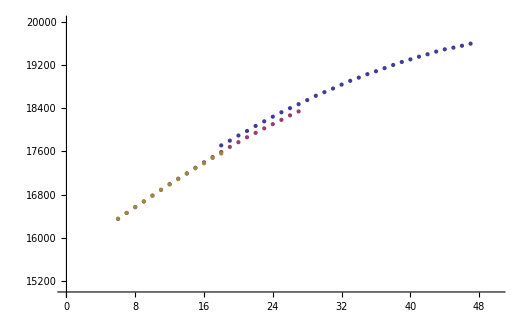

```mathematica
ListPlot[{Tooltip[ν0],Tooltip[ν1],Tooltip[ν2]},PlotRange->{{0,50},{15000,20000}}]
```

```mathematica
Δν0=Table[{ν0[[i,1]]+0.5,ν0[[i,2]]-ν0[[i+1,2]]},{i,1,Length[ν0]-1}]
Δν1=Table[{ν1[[i,1]]+0.5,ν1[[i,2]]-ν1[[i+1,2]]},{i,1,Length[ν1]-1}]
Δν2=Table[{ν2[[i,1]]+0.5,ν2[[i,2]]-ν2[[i+1,2]]},{i,1,Length[ν2]-1}]
```

{{47.5,38.6968},{46.5,35.1158},{45.5,30.8129},{44.5,42.0675},{43.5,49.7904},{42.5,45.0433},{41.5,48.934},{40.5,48.3164},{39.5,55.45},{38.5,58.4294},{37.5,57.7107},{36.5,54.1054},{35.5,63.8755},{34.5,59.5174},{33.5,69.7944},{32.5,72.0979},{31.5,67.704},{30.5,67.2172},{29.5,79.4749},{28.5,75.0462},{27.5,74.1028},{26.5,76.1972},{25.5,81.5607},{24.5,86.1137},{23.5,84.9779},{22.5,92.594},{21.5,84.9287},{20.5,94.9075},{19.5,87.6347}}

{{27.5,72.3625},{26.5,83.7045},{25.5,79.3362},{24.5,77.9971},{23.5,82.803},{22.5,81.7267},{21.5,91.4124},{20.5,87.0426},{19.5,93.9319},{18.5,94.7758},{17.5,95.2737},{16.5,101.126},{15.5,104.098},{14.5,99.054},{13.5,99.3636},{12.5,106.491},{11.5,106.01},{10.5,109.971},{9.5,104.697},{8.5,106.101},{7.5,111.17}}

{{18.5,83.4928},{17.5,97.8203},{16.5,93.1459},{15.5,98.6554},{14.5,101.624},{13.5,98.987},{12.5,99.273},{11.5,106.01},{10.5,105.522},{9.5,104.753},{8.5,110.494},{7.5,107.158}}

FittedModel[120.629-0.555977 (2+2 x)-0.00459212 (13/4+6 x+3 x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 120.629 | 13.6578 | 8.83225 | 2.63302×10^-9
b | 0.555977 | 0.411725 | 1.35036 | 0.188538
c | -0.00459212 | 0.00395491 | -1.16112 | 0.256143

(186.536 | 5.57572 | 0.0525625
5.57572 | 0.169517 | 0.00161887
0.0525625 | 0.00161887 | 0.0000156413)

(1. | 0.991547 | 0.973104
0.991547 | 1. | 0.994191
0.973104 | 0.994191 | 1.)

FittedModel[114.41-0.08749 (2+2 x)-0.0144986 (13/4+6 x+3 x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 114.41 | 7.05901 | 16.2076 | 3.50455×10^-12
b | 0.08749 | 0.408509 | 0.214169 | 0.832823
c | -0.0144986 | 0.00728343 | -1.99062 | 0.0619271

(49.8297 | 2.82701 | 0.0486189
2.82701 | 0.16688 | 0.00294419
0.0486189 | 0.00294419 | 0.0000530484)

(1. | 0.980351 | 0.945638
0.980351 | 1. | 0.989526
0.945638 | 0.989526 | 1.)

FittedModel[125.22-0.880083 (2+2 x)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 125.22 | 4.40963 | 28.397 | 6.82095×10^-11
b | 0.880083 | 0.152907 | 5.75567 | 0.000183739

(19.4449 | 0.654657
0.654657 | 0.0233806)

(1. | 0.97092
0.97092 | 1.)

120.087

0.50785

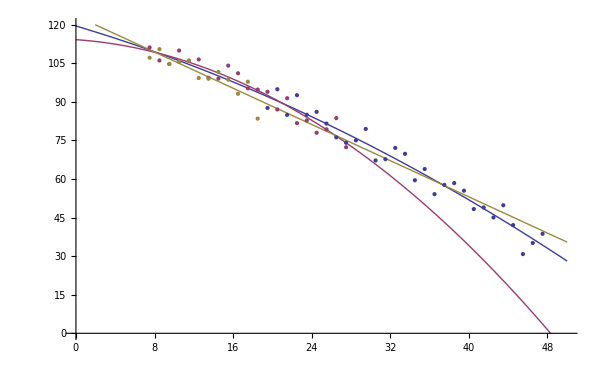

```mathematica
m0=NonlinearModelFit[Δν0,a- b(2x+2)+c (3 x^2+6x+13/4),{a,b,c},x]
m0["ParameterTable"]
m0["CovarianceMatrix"]//MatrixForm
m0["CorrelationMatrix"]//MatrixForm

m1=NonlinearModelFit[Δν1,a- b(2x+2)+c (3 x^2+6x+13/4),{a,b,c},x]
m1["ParameterTable"]
m1["CovarianceMatrix"]//MatrixForm
m1["CorrelationMatrix"]//MatrixForm

m2=NonlinearModelFit[Δν2,a- b(2x+2),{a,b},x]
m2["ParameterTable"]
m2["CovarianceMatrix"]//MatrixForm
m2["CorrelationMatrix"]//MatrixForm

(m0["ParameterTableEntries"][[1,1]]+m1["ParameterTableEntries"][[1,1]]+m2["ParameterTableEntries"][[1,1]])/3
(m0["ParameterTableEntries"][[2,1]]+m1["ParameterTableEntries"][[2,1]]+m2["ParameterTableEntries"][[2,1]])/3

Show[Plot[{Normal[m0],Normal[m1],Normal[m2]},{x,0,50},PlotRange->{{0,50},{0,120}}],ListPlot[{Δν0,Δν1,Δν2}]]
```

FittedModel[136.061-1.03126 (2+2 x)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 136.061 | 3.16654 | 42.9683 | 2.13037×10^-26
b | 1.03126 | 0.0445992 | 23.1229 | 2.49823×10^-19

(10.027 | 0.137247
0.137247 | 0.00198909)

(1. | 0.971831
0.971831 | 1.)

FittedModel[127.698-0.89216 (2+2 x)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 127.698 | 2.46825 | 51.7362 | 6.53312×10^-22
b | 0.89216 | 0.0633997 | 14.072 | 1.68336×10^-11

(6.09226 | 0.148722
0.148722 | 0.00401953)

(1. | 0.950386
0.950386 | 1.)

FittedModel[125.22-0.880083 (2+2 x)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 125.22 | 4.40963 | 28.397 | 6.82095×10^-11
b | 0.880083 | 0.152907 | 5.75567 | 0.000183739

(19.4449 | 0.654657
0.654657 | 0.0233806)

(1. | 0.97092
0.97092 | 1.)

129.66

0.934501

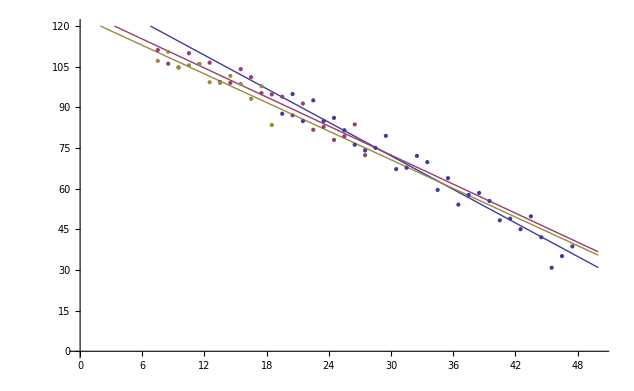

```mathematica
m0=NonlinearModelFit[Δν0,a- b(2x+2),{a,b},x]
m0["ParameterTable"]
m0["CovarianceMatrix"]//MatrixForm
m0["CorrelationMatrix"]//MatrixForm

m1=NonlinearModelFit[Δν1,a- b(2x+2),{a,b},x]
m1["ParameterTable"]
m1["CovarianceMatrix"]//MatrixForm
m1["CorrelationMatrix"]//MatrixForm

m2=NonlinearModelFit[Δν2,a- b(2x+2),{a,b},x]
m2["ParameterTable"]
m2["CovarianceMatrix"]//MatrixForm
m2["CorrelationMatrix"]//MatrixForm

(m0["ParameterTableEntries"][[1,1]]+m1["ParameterTableEntries"][[1,1]]+m2["ParameterTableEntries"][[1,1]])/3
(m0["ParameterTableEntries"][[2,1]]+m1["ParameterTableEntries"][[2,1]]+m2["ParameterTableEntries"][[2,1]])/3

Show[Plot[{Normal[m0],Normal[m1],Normal[m2]},{x,0,50},PlotRange->{{0,50},{0,120}}],ListPlot[{Δν0,Δν1,Δν2}]]
```